```mathematica
data = Import["PATH-TO-FILE-GOES-HERE\\raw_extracted_data.xlsx"]
```

{{{0.,9.19},{0.0167,23.},{0.0333,60.8},{0.05,118.},{0.0667,194.},{0.0833,286.},{0.1,388.},{0.117,496.},{0.133,605.},{0.15,708.},{0.167,797.},{0.183,866.},{0.2,904.},{0.217,903.},{0.233,864.},{0.25,787.},{0.267,683.},{0.283,559.},{0.3,422.},{0.317,289.},{0.333,172.},{0.35,90.4},{0.367,34.9},{0.383,8.92},{0.4,13.1},{0.417,43.},{0.433,95.},{0.45,165.},{0.467,251.},{0.483,348.},{0.5,454.},{0.517,562.},{0.533,669.},{0.55,764.},{0.567,842.},{0.583,892.},{0.6,905.},{0.617,880.},{0.633,818.},{0.65,724.},{0.667,605.},{0.683,473.},{0.7,337.},{0.717,213.},{0.733,115.},{0.75,51.8},{0.767,13.4},{0.783,6.48},{0.8,26.6},{0.817,71.2},{0.833,133.},{0.85,214.},{0.867,308.},{0.883,410.},{0.9,518.},{0.917,626.},{0.933,728.},{0.95,814.},{0.967,875.},{0.983,902.},{1.,891.},{1.02,844.},{1.03,761.},{1.05,652.},{1.07,524.},{1.08,387.},{1.1,257.},{1.12,147.},{1.13,75.1},{1.15,25.3},{1.17,6.89},{1.18,17.5},{1.2,52.7},{1.22,108.},{1.23,182.},{1.25,273.},{1.27,372.},{1.28,479.},{1.3,589.},{1.32,694.},{1.33,786.},{1.35,857.},{1.37,897.},{1.38,899.},{1.4,865.},{1.42,793.},{1.43,693.},{1.45,570.},{1.47,434.},{1.48,300.},{1.5,180.},{1.52,94.6},{1.53,36.5},{1.55,6.92},{1.57,7.19},{1.58,32.8},{1.6,83.3},{1.62,151.},{1.63,235.},{1.65,332.},{1.67,436.},{1.68,546.},{1.7,655.},{1.72,752.},{1.73,831.},{1.75,883.},{1.77,899.},{1.78,879.},{1.8,822.},{1.82,732.},{1.83,616.},{1.85,483.},{1.87,345.},{1.88,220.},{1.9,120.},{1.92,54.2},{1.93,12.9},{1.95,3.31},{1.97,19.3},{1.98,60.8},{2.,122.},{2.02,202.},{2.03,295.},{2.05,397.},{2.07,506.},{2.08,614.},{2.1,718.},{2.12,802.},{2.13,864.},{2.15,894.},{2.17,886.},{2.18,843.},{2.2,765.},{2.22,658.},{2.23,529.},{2.25,390.},{2.27,260.},{2.28,150.},{2.3,75.2},{2.32,22.5},{2.33,1.54},{2.35,8.81},{2.37,42.5},{2.38,96.8},{2.4,172.},{2.42,260.},{2.43,358.},{2.45,465.},{2.47,574.},{2.48,679.},{2.5,770.},{2.52,840.},{2.53,884.},{2.55,892.},{2.57,863.},{2.58,796.},{2.6,700.},{2.62,578.},{2.63,442.},{2.65,308.},{2.67,191.},{2.68,102.},{2.7,43.},{2.72,12.4},{2.73,10.9},{2.75,36.3},{2.77,84.8},{2.78,151.},{2.8,235.},{2.82,329.},{2.83,433.},{2.85,542.},{2.87,650.},{2.88,746.},{2.9,824.},{2.92,878.},{2.93,897.},{2.95,880.},{2.97,826.},{2.98,735.},{3.,618.},{3.02,484.},{3.03,348.},{3.05,224.},{3.07,123.},{3.08,55.8},{3.1,14.8},{3.12,4.18},{3.13,20.2},{3.15,61.1},{3.17,121.},{3.18,199.},{3.2,291.},{3.22,392.},{3.23,501.},{3.25,608.},{3.27,710.},{3.28,795.},{3.3,858.},{3.32,891.},{3.33,886.},{3.35,845.},{3.37,764.},{3.38,657.},{3.4,527.},{3.42,390.},{3.43,261.},{3.45,150.},{3.47,75.5},{3.48,22.3},{3.5,0.143},{3.52,6.55},{3.53,40.3},{3.55,93.6},{3.57,164.},{3.58,251.},{3.6,350.},{3.62,455.},{3.63,564.},{3.65,669.},{3.67,762.},{3.68,835.},{3.7,881.},{3.72,891.},{3.73,863.},{3.75,796.},{3.77,698.},{3.78,575.},{3.8,439.},{3.82,305.},{3.83,186.},{3.85,97.4},{3.87,34.7},{3.88,0.811},{3.9,-2.29},{3.92,21.3},{3.93,68.3},{3.95,133.},{3.97,215.},{3.99,309.},{4.,412.},{4.02,520.},{4.04,626.},{4.05,725.},{4.07,808.},{4.09,865.},{4.1,888.},{4.12,873.},{4.14,821.},{4.15,733.},{4.17,618.},{4.19,486.},{4.2,350.},{4.22,224.},{4.24,121.},{4.25,51.1},{4.27,6.32},{4.29,-7.95},{4.3,5.37},{4.32,44.7},{4.34,103.},{4.35,178.},{4.37,270.},{4.39,371.},{4.4,479.},{4.42,587.},{4.44,690.},{4.45,780.},{4.47,848.},{4.49,884.},{4.5,883.},{4.52,845.},{4.54,769.},{4.55,663.},{4.57,536.},{4.59,400.},{4.6,269.},{4.62,155.},{4.64,77.9},{4.65,22.1},{4.67,-4.15},{4.69,-0.449},{4.7,29.9},{4.72,82.},{4.74,150.},{4.75,237.},{4.77,335.},{4.79,439.},{4.8,547.},{4.82,654.},{4.84,751.},{4.85,829.},{4.87,877.},{4.89,888.},{4.9,863.},{4.92,800.},{4.94,704.},{4.95,584.},{4.97,450.},{4.99,315.},{5.,193.},{5.02,101.},{5.04,38.4},{5.05,0.86},{5.07,-5.29},{5.09,15.6},{5.1,59.4},{5.12,121.},{5.14,202.},{5.15,297.},{5.17,399.},{5.19,506.},{5.2,614.},{5.22,716.},{5.24,802.},{5.25,861.},{5.27,886.},{5.29,874.},{5.3,825.},{5.32,740.},{5.34,628.},{5.35,498.},{5.37,362.},{5.39,235.},{5.4,129.},{5.42,55.2},{5.44,12.3},{5.45,2.04},{5.47,2.04},{5.49,26.6},{5.5,99.},{5.52,172.},{5.54,263.},{5.55,362.},{5.57,469.},{5.59,577.},{5.6,683.},{5.62,774.},{5.64,844.},{5.65,879.},{5.67,879.},{5.69,844.},{5.7,771.},{5.72,669.},{5.74,545.},{5.75,408.},{5.77,275.},{5.79,160.},{5.8,82.1},{5.82,24.8},{5.84,-4.33},{5.85,-3.12},{5.87,24.4},{5.89,75.5},{5.9,143.},{5.92,228.},{5.94,325.},{5.95,429.},{5.97,537.},{5.99,645.},{6.,744.},{6.02,821.},{6.04,870.},{6.05,884.},{6.07,862.},{6.09,804.},{6.1,713.},{6.12,595.},{6.14,462.},{6.15,326.},{6.17,204.},{6.19,108.},{6.2,44.4},{6.22,3.28},{6.24,-6.34},{6.25,12.},{6.27,54.3},{6.29,116.},{6.3,196.},{6.32,289.},{6.34,390.},{6.35,498.},{6.37,607.},{6.39,710.},{6.4,796.},{6.42,856.},{6.44,883.},{6.45,875.},{6.47,830.},{6.49,749.},{6.5,640.},{6.52,510.},{6.54,373.},{6.55,243.},{6.57,136.},{6.59,47.},{6.6,14.3},{6.62,-2.04},{6.64,12.3},{6.65,33.5},{6.67,91.2},{6.69,161.},{6.7,251.},{6.72,350.},{6.74,456.},{6.75,565.},{6.77,671.},{6.79,763.},{6.8,833.},{6.82,873.},{6.84,879.},{6.85,851.},{6.87,784.},{6.89,685.},{6.9,562.},{6.92,426.},{6.94,293.},{6.95,175.},{6.97,92.6},{6.99,31.6},{7.,-2.77},{7.02,-4.56},{7.04,21.2},{7.05,70.5},{7.07,136.},{7.09,219.},{7.1,314.},{7.12,418.},{7.14,527.},{7.15,634.},{7.17,732.},{7.19,812.},{7.2,864.},{7.22,882.},{7.24,866.},{7.25,812.},{7.27,723.},{7.29,606.},{7.3,473.},{7.32,335.},{7.34,211.},{7.35,111.},{7.37,43.9},{7.39,-1.13},{7.4,-13.},{7.42,2.81},{7.44,44.2},{7.45,104.},{7.47,181.},{7.49,274.},{7.5,374.},{7.52,482.},{7.54,591.},{7.55,693.},{7.57,781.},{7.59,845.},{7.6,878.},{7.62,875.},{7.64,836.},{7.65,757.},{7.67,651.},{7.69,522.},{7.7,385.},{7.72,255.},{7.74,144.},{7.75,75.7},{7.77,34.8},{7.79,2.04},{7.8,6.13},{7.82,28.6},{7.84,84.6},{7.85,152.},{7.87,240.},{7.89,337.},{7.9,443.},{7.92,551.},{7.94,657.},{7.95,751.},{7.97,825.},{7.99,871.},{8.,881.},{8.02,854.},{8.04,790.},{8.05,691.},{8.07,569.},{8.09,433.},{8.1,298.},{8.12,178.},{8.14,92.3},{8.15,27.6},{8.17,-10.},{8.19,-14.6},{8.2,8.09},{8.22,54.6},{8.24,119.},{8.25,199.},{8.27,294.},{8.29,397.},{8.3,504.},{8.32,611.},{8.34,712.},{8.35,795.},{8.37,854.},{8.39,879.},{8.4,867.},{8.42,818.},{8.44,733.},{8.45,618.},{8.47,487.},{8.49,350.},{8.5,224.},{8.52,120.},{8.54,69.5},{8.55,16.4},{8.57,-10.2},{8.59,12.3},{8.6,59.3},{8.62,98.5},{8.64,172.},{8.65,263.},{8.67,363.},{8.69,470.},{8.7,578.},{8.72,682.},{8.74,772.},{8.75,840.},{8.77,876.},{8.79,876.},{8.8,839.},{8.82,763.},{8.84,658.},{8.85,531.},{8.87,395.},{8.89,263.},{8.9,148.},{8.92,61.3},{8.94,4.09},{8.95,-16.4},{8.97,20.4},{8.99,42.9},{9.,73.6},{9.02,136.},{9.04,222.},{9.05,319.},{9.07,424.},{9.09,531.},{9.1,638.},{9.12,735.},{9.14,814.},{9.15,864.},{9.17,877.},{9.19,855.},{9.2,793.},{9.22,700.},{9.24,580.},{9.25,447.},{9.27,312.},{9.29,190.},{9.3,98.7},{9.32,40.9},{9.34,16.4},{9.35,-6.13},{9.37,34.8},{9.39,65.4},{9.4,112.},{9.42,191.},{9.44,284.},{9.45,386.},{9.47,493.},{9.49,601.},{9.5,703.},{9.52,789.},{9.54,850.},{9.55,876.},{9.57,865.},{9.59,818.},{9.6,735.},{9.62,624.},{9.64,494.},{9.65,357.},{9.67,229.},{9.69,123.}}}

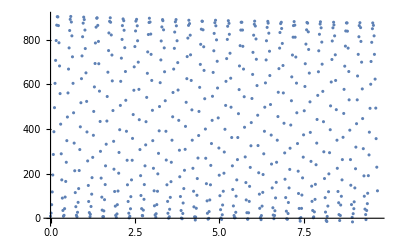

```mathematica
ListPlot[data[[1]]]
```

FittedModel[424.812+444.007 Sin[4.83312-16.1279 x]]

| Estimate | Standard Error | Confidence Interval
a | -444.007 | 1.65659 | {-447.261,-440.753}
b | 16.1279 | 0.00132833 | {16.1253,16.1306}
c | 424.812 | 1.17092 | {422.513,427.112}
d | -4.83312 | 0.00746105 | {-4.84777,-4.81846}

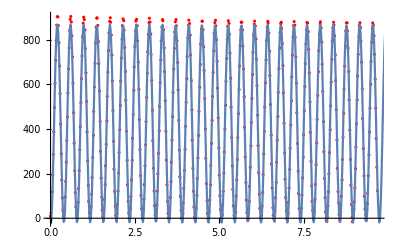

```mathematica
(*use a fit model to determine the frequency of oscillation*)
(*a: amplitude, b: angular frequency, x: time (x-coord), d: phase, c: amplitude offset*)
model=a*Sin[b*x+d]+c;
(*an initial guess required before performing the fit*)
fit=NonlinearModelFit[data[[1]],model,{{a,50},{b,19},{c,-190},{d,1.5}},x, Method->NMinimize]
fit["ParameterConfidenceIntervalTable"]
Show[ListPlot[data[[1]],PlotStyle->Red],Plot[fit[x],{x,0,67}]]
```